## Project 7 Javier Salazar 1001144647.

Survival of Family Names.  One quarter of married couples in certain society have no children.  The other three quarters have exactly three children, each equally likely to be a boy or a girl. Using the Branching Processes model
  
(a)  Find the PGF (Probability Generating Function)  φ(s)

```mathematica
Clear[s];Solve[s==11/32+ s 9/32+s^2 9/32 +s^3 3/32,s];
```

(b)  Graph  φ(s)  together with the function g(s) = s.

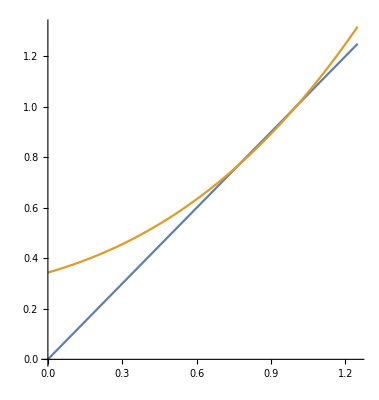

```mathematica
Plot[{s,11/32+ s 9/32+s^2 9/32 +s^3 3/32},{s,0,1.25},AspectRatio->Automatic]
```

(c)  Find the expected size of the male population in the 7-th generation.

```mathematica
Print["The expected size of the male population in the 7-th generation is ",(9/8)^7//N]
```

The expected size of the male population in the 7-th generation is 2.2807

(d)  What is the probability that the male line of descent of a particular husband will die out

       (i)    in the 3-rd  generation

```mathematica
π1=11/32//N;
π2=11/32+ π1 9/32+π1^2 9/32+ π1^3 3/32//N;
π3=11/32+ π2 9/32+π2^2 9/32+ π2^3 3/32//N;
Print["The probability that the male descent of a particular husband will die out in the 3-rd generation is ",π3-π2]
```

The probability that the male descent of a particular husband will die out in the 3-rd generation is 0.0748915

(ii)   by the 7-th generation

```mathematica
π1=11/32//N;
π2=11/32+ π1 9/32+π1^2 9/32+ π1^3 3/32//N;
π3=11/32+ π2 9/32+π2^2 9/32+ π2^3 3/32//N;
π4=11/32+ π3 9/32+π3^2 9/32+ π3^3 3/32//N;
π5=11/32+ π4 9/32+π4^2 9/32+ π4^3 3/32//N;
π6=11/32+ π5 9/32+π5^2 9/32+ π5^3 3/32//N;
π7=11/32+ π6 9/32+π6^2 9/32+ π6^3 3/32//N;
Print["The probability that the male descent of a particular husband will die out by the 7-th generation is ",π7]
```

The probability that the male descent of a particular husband will die out by the 7-th generation is 0.678367

(iii)  eventually

```mathematica
extinct=11/32;
For[i=2,i≤100000,i++,extinct=(11/32+ extinct 9/32+extinct^2 9/32+ extinct^3 3/32)//N]
Print["The probability that the male descent of a particular husband will die out eventually is ",extinct]
```

The probability that the male descent of a particular husband will die out eventually is 0.768875

(e)  Simulate n = 100000 samples of the first 7 male generations, compute the frequency of extinction by 
      the 7-th generation and the average size of the 7-th generation of males. Compare with exact values.

Hint. Use total probability formula to determine the probabilities of a father having  k  boys  P_k , k = 0, 1, 2, 3.

```mathematica
Plot[Piecewise[{{0,0≤x≤ 11/32},{1,11/32<x≤ 20/32},{2,20/32<x≤ 29/32},{3,29/32<x≤1}}],{x,0,1}];
```

```mathematica
X:=RandomReal[]
g[x_]:=Piecewise[{{0,0≤x≤ 11/32},{1,11/32<x≤ 20/32},{2,20/32<x≤ 29/32},{3,29/32<x≤1}}]
n=100000;NumGenerations=7;size=0;count1=0;
Do[ x=1;
  Do[
       If[x>0,a=Table[g[X],{x}];x=Apply[Plus,a]],
      {NumGenerations}];
  If[x==0,count1=count1+1,size=size+x ],
 {n}];
Print["frequency(extinction by 7-th generation) = ",count1/n//N];
Print["π_7= ", 0.678367];
Print["average(size of 7-th generation) = ",( size/n)//N];
Print["E X_7 = ",(9/8)^7//N];
```

frequency(extinction by 7-th generation) = 0.67647

π_7= 0.678367

average(size of 7-th generation) = 2.29617

E X_7 = 2.2807

2. Survival of Family Names(B).  Married couple in certain society have  no children, one child or 2 children with equal probabilities. 
    Each child is equally likely to be a boy or a girl.
    
    (a)  Find the PGF (Probability Generating Function)  φ(s)

```mathematica
Clear[s];Solve[s== 7/12+s 4/12+ +s^2 1/12,s];
```

(b)  Graph  φ(s)  together with the function g(s) = s.

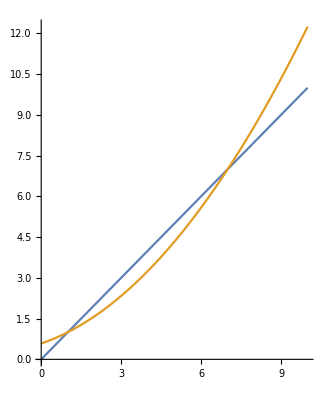

```mathematica
Plot[{s,7/12+s 4/12+ +s^2 1/12},{s,0,10},AspectRatio->Automatic]
```

(c)  Find the expected size of the male population in the 7-th generation.

```mathematica
Print["The expected size of the male population in the 7-th generation is ",(1/2)^7//N]
```

The expected size of the male population in the 7-th generation is 0.0078125

(d)  What is the probability that the male line of descent of a particular husband will die out

       (i)    in the 3-rd  generation

```mathematica
π1=7/12//N;
π2=7/12+ π1 4/12+π1^2 1/12//N;
π3=7/12+π2 4/12+ π2^2 1/12//N;
Print["The probability that the male descent of a particular husband will die out in the 3-rd generation is ",π3-π2]
```

The probability that the male descent of a particular husband will die out in the 3-rd generation is 0.100065

(ii)   by the n-th generation for n = 1, 2, 3, 4, 5, 6, 7, 8, 9, 10

```mathematica
π1=7/12//N
π2=7/12+ π1 4/12+π1^2 1/12//N
π3=7/12+ π2 4/12+π2^2 1/12//N
π4=7/12+ π3 4/12+π3^2 1/12//N
π5=7/12+ π4 4/12+π4^2 1/12//N
π6=7/12+ π5 4/12+π5^2 1/12//N
π7=7/12+ π6 4/12+π6^2 1/12//N
π8=7/12+ π7 4/12+π7^2 1/12//N
π9=7/12+ π8 4/12+π8^2 1/12//N
π10=7/12+ π9 4/12+π9^2 1/12//N
```

0.583333

0.806134

0.906199

0.953833

0.977094

0.988591

0.994306

0.997156

0.998579

0.999289

(iii)  eventually

```mathematica
extinct=7/12;
For[i=2,i≤100000,i++,extinct=(7/12+extinct 4/12+ extinct^2 1/12)//N]
Print["The probability that the male descent of a particular husband will die out eventually is ",extinct]
```

The probability that the male descent of a particular husband will die out eventually is 1.

(e)  Simulate n = 100000 samples of the first 7 male generations, compute the frequency of extinction by 
      the 7-th generation and the average size of the 7-th generation of males. Compare with exact values.

```mathematica
X:=RandomReal[]
g[x_]:=Piecewise[{{0,0≤x≤ 7/12},{1,7/12<x≤ 11/12},{2,11/12<x≤ 1}}]
n=100000;NumGenerations=7;size=0;count1=0;
Do[ x=1;
  Do[
       If[x>0,a=Table[g[X],{x}];x=Apply[Plus,a]],
      {NumGenerations}];
  If[x==0,count1=count1+1,size=size+x ],
 {n}];
Print["frequency(extinction by 7-th generation) = ",count1/n//N];
Print["π_7= ", 0.99431];
Print["average(size of 7-th generation) = ",( size/n)//N];
Print["E X_7 = ",(1/2)^7//N];
```

frequency(extinction by 7-th generation) = 0.99445

π_7= 0.99431

average(size of 7-th generation) = 0.00757

E X_7 = 0.0078125

3. Survival of Family Tree.  Assume that the number of children of a given family in certain region (along will all decedents of future
   generations) follows binomial distribution b(5,1/2).
   
(a)  Find the PGF (Probability Generating Function)  φ(s).

```mathematica
Clear[s];Solve[s== 0.03125+s*0.15625 +s^2 0.3125+s^3 0.3125+s^4 0.15625+s^5 0.03125,s];
```

(b)  Graph  φ(s)  together with the function g(s) = s.

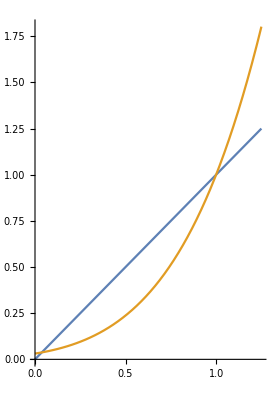

```mathematica
Plot[{s, 0.03125+s*0.15625 +s^2 0.3125+s^3 0.3125+s^4 0.15625+s^5 0.03125},{s,0,1.25},AspectRatio->Automatic]
```

(c)  Find the expected size of  population in the 10-th generation.

```mathematica
Print["The expected size of the population in the 7-th generation is ",(2.5)^10//N]
```

The expected size of the population in the 7-th generation is 9536.74

(d)  What is the probability that the family dies out

       (i)    in the 10-rd  generation

```mathematica
π1=0.03125;
π2=0.03125+ π1*0.15625+π1^2*0.3125+π1^3*0.3125+π1^4*0.15625+π1^5*0.03125;
π3=0.03125+ π2*0.15625+π2^2*0.3125+π2^3*0.3125+π2^4*0.15625+π2^5*0.03125;
π4=0.03125+ π3*0.15625+π3^2*0.3125+π3^3*0.3125+π3^4*0.15625+π3^5*0.03125;
π5=0.03125+ π4*0.15625+π4^2*0.3125+π4^3*0.3125+π4^4*0.15625+π4^5*0.03125;
π6=0.03125+ π5*0.15625+π5^2*0.3125+π5^3*0.3125+π5^4*0.15625+π5^5*0.03125;
π7=0.03125+ π6*0.15625+π6^2*0.3125+π6^3*0.3125+π6^4*0.15625+π6^5*0.03125;
π8=0.03125+ π7*0.15625+π7^2*0.3125+π7^3*0.3125+π7^4*0.15625+π7^5*0.03125;
π9=0.03125+ π8*0.15625+π8^2*0.3125+π8^3*0.3125+π8^4*0.15625+π8^5*0.03125;
π10=0.03125+ π9*0.15625+π9^2*0.3125+π9^3*0.3125+π9^4*0.15625+π9^5*0.03125;
Print["The probability that the family will die out in the 10-th generation is ",π10-π9]
```

The probability that the family will die out in the 10-th generation is 5.90803×10^-9

(ii)   by the 10-th generation

```mathematica
Print["The probability that the family will die out by the 10-th generation is ",π10]
```

The probability that the family will die out by the 10-th generation is 0.0375801

(iii)  eventually                            ( Hint. Use  NRoots[ . ] or Solve [ . ] )

```mathematica
extinct=0.03125;
For[i=2,i≤100000,i++,extinct=(0.03125+ extinct*0.15625+extinct^2*0.3125+extinct^3*0.3125+extinct^4*0.15625+extinct^5*0.03125)//N]
Print["The probability that the family will die out eventually is ",extinct]
```

The probability that the family will die out eventually is 0.0375801

(e)  Simulate n = 100000 samples of the first 10 generations, compute the frequency of extinction by 
      the 10-th generation and the average size and standard deviation of the 10-th generation of males . 
      Compare with exact values.

```mathematica
X:=RandomReal[]
h[x_]:=Piecewise[{{0,0≤x≤ 0.03125},{1,0.03125<x≤ 0.1875},{2,0.1875<x≤0.5},{3,0.5<x≤0.8125},{4,0.8125<x≤0.96875},{5,0.96875<x≤1}}]
n=100000;NumGenerations=10;size=0;count1=0;
Do[ x=1;
  Do[
       If[x>0,a=Table[h[X],{x}];x=Apply[Plus,a]],
      {NumGenerations}];
  If[x==0,count1=count1+1,size=size+x ],
 {n}];
Print["frequency(extinction by 10-th generation) = ",count1/n//N];
Print["π_10= ", 0.0375801];
Print["average(size of 10-th generation) = ",( size/n)//N];
Print["E X_10 = ",(2.5)^10//N];
```

frequency(extinction by 10-th generation) = 0.03746

π_10= 0.0375801

average(size of 10-th generation) = 9533.54

E X_10 = 9536.74